# Effective Potentials of Kerr BHs embedded in a swirling universe

This notebooks implements the procedure first developed by Cunha, Grover, et alia (https://arxiv.org/abs/1609.01340) in 2016 to a Kerr Black Hole embedded in a swirling background. We begin by setting up the metric before calculating the effective potentials, as described in (Cunha 2016) before plotting these contours for varying parameters a and j. We can clearly see the formation of pockets for certain values of a and j indicating chaotic motion in these regions. Again this is described in the above cited paper.

Author: E.A.G. Murray

## Coordinates & Metric:

Setting  up  the  coordinate  system, metric  and  inverse  metric  which  will  be  used  throughout

```mathematica
Δ =r^2-2 M r+a^2;
R=r^2+a^2(Cos[θ])^2;
ρ=(Δ*(Sin[θ])^2)^(1/2);
Σ=(r^2+a^2)-Δ*a^2*(Sin[θ])^2;
Ω=Δ*a*(Cos[θ])^2;
Ξ=r^2((Cos[θ])^2-3)+a^2(1+(Cos[θ])^2);

f0=R^4;
f1 =4 a*M*Ξ*Cos[θ] R^2;
f2=4 a^2 M^2 Ξ^2(Cos[θ])^2+Σ^2(Sin[θ])^4;
w0 = 2 a M r;
w1 =4(Cos[θ])(M a^4-r^4(r-2M)-Δ*a^2 r-a(r-M)Ω);
w2= 2M(3a r^5-a^5(r+2M)+2 a^3 r^2(r+3M)-r^3((Cos[θ])^2-6)Ω+a^2 Ω((Cos[θ])^2)(3r-2M)-6(r-M));
```

```mathematica
f =Simplify[ (f0+j*f1+j^2 f2)/(R^2 Σ(Sin[θ])^2)];
w=Simplify[(w0+j w1+j^2 w2)/Σ];
```

```mathematica
coordinates = {t,r,θ,ϕ};
metric = {{w^2/f-ρ^2 f,0,0,w/f},{0,(f*Σ*(Sin[θ])^2)/Δ,0,0},{0,0,f*Σ*(Sin[θ])^2,0},{w/f,0,0,1/f}};
invMetric= Inverse[metric];
```

```mathematica
invMetric[[3,3]]
```

Csc[θ]^2/(f Σ)

```mathematica
metric[[3,3]]
```

f Σ Sin[θ]^2

## Effective Potentials

Inputted explicitly in this case, for formula see (Cunha 2016)

```mathematica
hPlus = Simplify[-1/(w+f ρ)];
```

```mathematica
hMinus =Simplify [-1/(w-f ρ)];
```

```mathematica
metric[[1,1]]
```

((r^2+a^2 Cos[θ]^2)^2 (2 a M r+4 j Cos[θ] (a^4 M-r^4 (-2 M+r)-a^2 r (a^2+r (-2 M+r))+a^2 (M-r) (a^2+r (-2 M+r)) Cos[θ]^2)+2 j^2 M (6 (M-r)+3 a r^5-a^5 (2 M+r)+2 a^3 r^2 (3 M+r)+a^3 (-2 M+3 r) (a^2+r (-2 M+r)) Cos[θ]^4-a r^3 (a^2+r (-2 M+r)) Cos[θ]^2 (-6+Cos[θ]^2)))^2 Sin[θ]^2)/((a^2+r^2-a^2 (a^2+r (-2 M+r)) Sin[θ]^2) ((r^2+a^2 Cos[θ]^2)^4+4 a j M Cos[θ] (r^2+a^2 Cos[θ]^2)^2 (a^2-3 r^2+(a^2+r^2) Cos[θ]^2)+j^2 (4 a^2 M^2 Cos[θ]^2 (a^2-3 r^2+(a^2+r^2) Cos[θ]^2)^2+Sin[θ]^4 (a^2+r^2-a^2 (a^2+r (-2 M+r)) Sin[θ]^2)^2)))-((a^2-2 M r+r^2) ((r^2+a^2 Cos[θ]^2)^4+4 a j M Cos[θ] (r^2+a^2 Cos[θ]^2)^2 (a^2-3 r^2+(a^2+r^2) Cos[θ]^2)+j^2 (4 a^2 M^2 Cos[θ]^2 (a^2-3 r^2+(a^2+r^2) Cos[θ]^2)^2+Sin[θ]^4 (a^2+r^2-a^2 (a^2+r (-2 M+r)) Sin[θ]^2)^2)))/((r^2+a^2 Cos[θ]^2)^2 (a^2+r^2-a^2 (a^2+r (-2 M+r)) Sin[θ]^2))

## Contour Plots

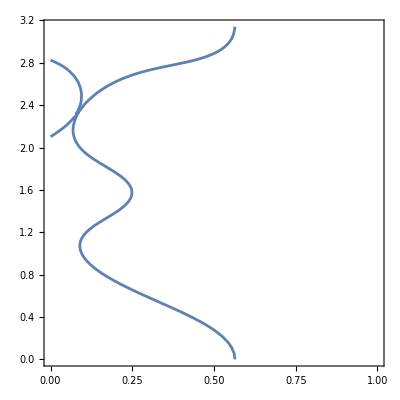

```mathematica
Clear[{a,M,j}]
a=0.9;
M=1;
j=0.1;
ContourPlot[metric[[1,1]]==0,{r,0,1},{θ,0,π}]
```

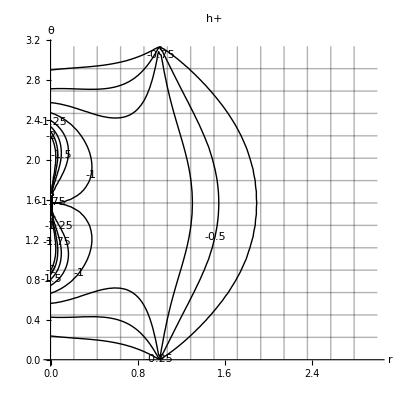

```mathematica
Clear[{a,M,j}]
ContourPlot[hPlus/.{M-> 1,a->1,j-> 0},{r,0,3},{θ,0,π},Frame-> False, Axes-> True,ContourLabels-> All,ContourShading->None,AxesLabel->{r,θ},Mesh->Full,PlotLegends->Automatic,PlotLabel->"h+"]
```

```mathematica
Plot3D[hPlus/.{M->1,a->1,j->4},{r,0,2},{θ,0,π},ColorFunction->"Rainbow",PlotLegends->Automatic,PlotTheme->"Classic"]
```

-Graphics3D-

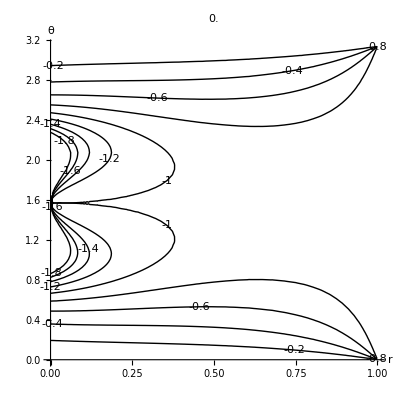
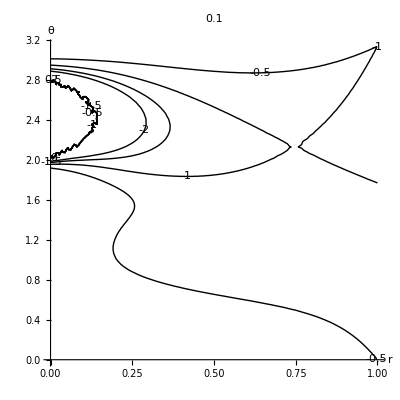
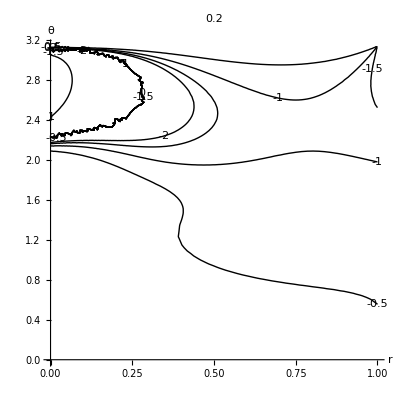
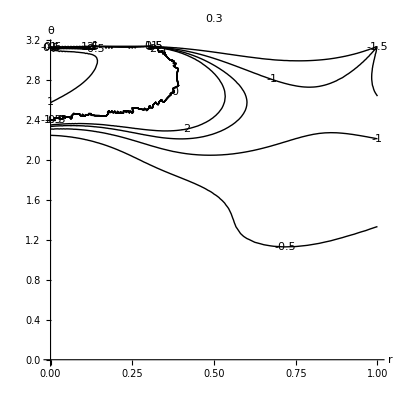
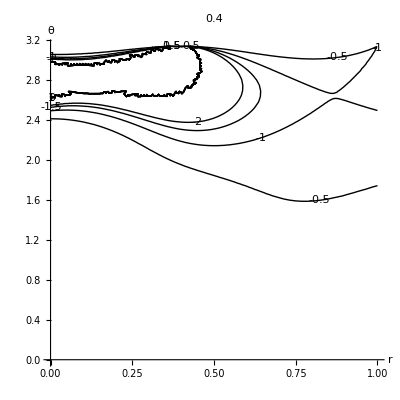
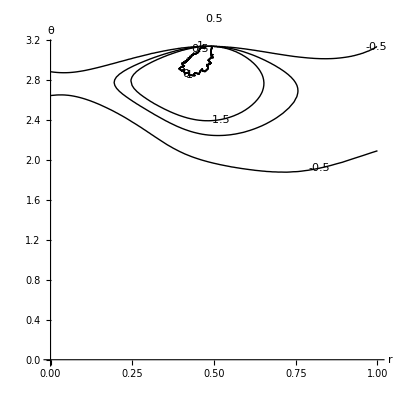
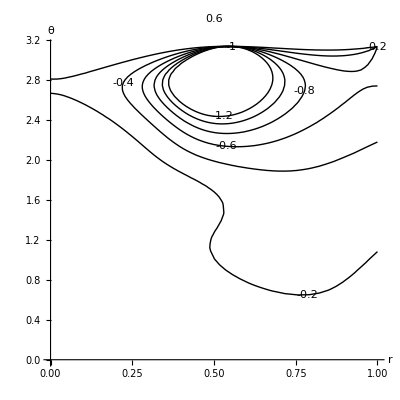
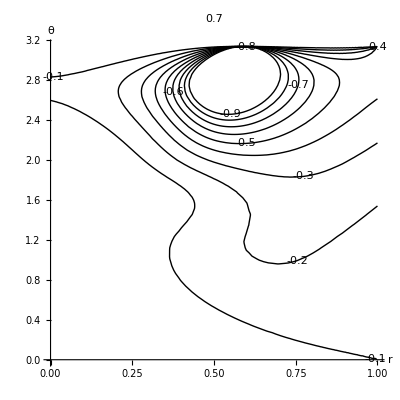

```mathematica
hplusPlots=Table[ContourPlot[hPlus/.{M-> 1,a-> 1},{r,0,1},{θ,0,π},ContourLabels->All,Frame-> False, Axes-> True,AxesLabel->{r,θ},ContourShading->None, PlotLegends->Automatic,PlotLabel->j],{j,0,1,0.1}]
```

```mathematica
Table[Plot3D[hPlus/.{M-> 1,a-> 1},{r,0,1},{θ,0,π},PlotLabel->j],{j,0,1,0.1}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

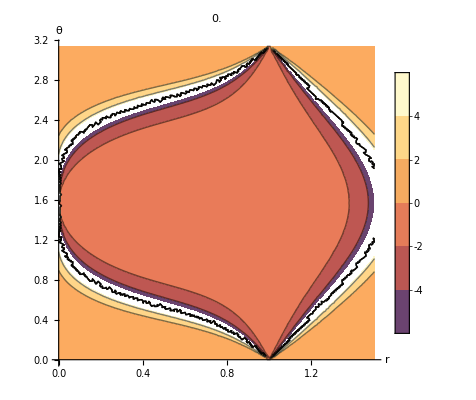
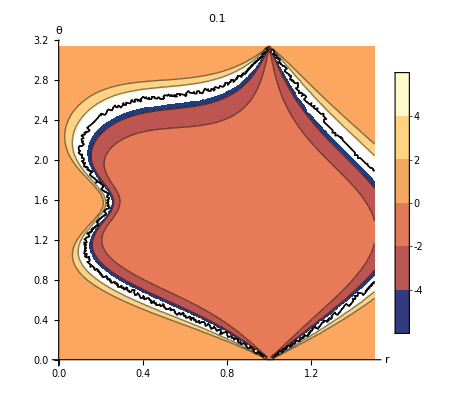
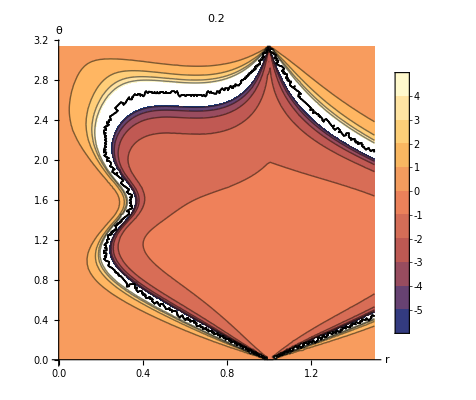
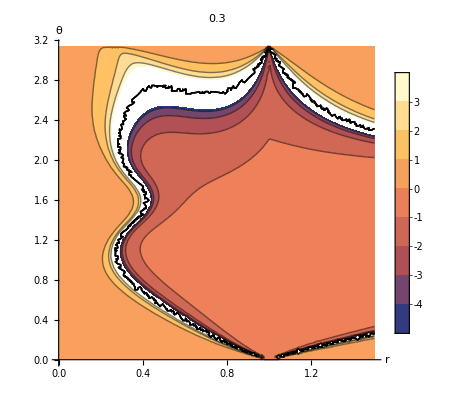
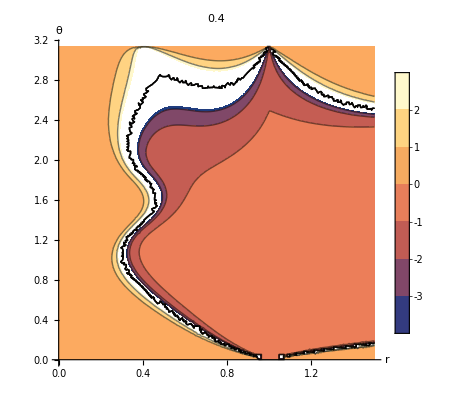
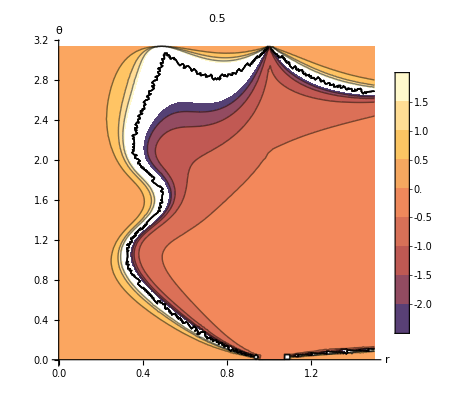
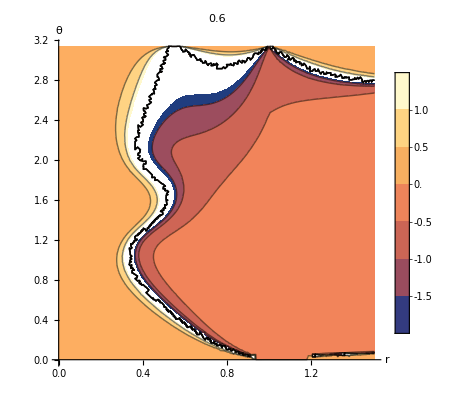
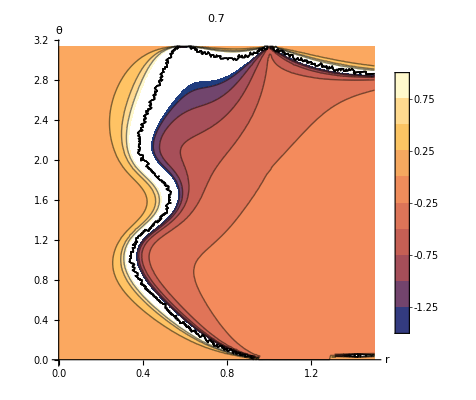
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
hMinusPlots=Table[ContourPlot[hMinus/.{M-> 1,a-> 1},{r,0,1.5},{θ,0,π},Frame-> False, Axes-> True,AxesLabel->{r,θ},PlotLegends->Automatic,PlotLabel->j],{j,0,1,0.1}]
```

```mathematica
ContourPlot[hMinus/.{M-> 1,a-> 1,j-> 1},{r,0.5406,0.5407},{θ,1.511,1.512}]
```

-Graphics-